```mathematica
(* Constants of Nature *)
(*$MinPrecision=5; (* allowed for print outs *)*)
lowestprec=30; (* might not specify precision, but using machine precision may not be enough.  Also, even if use more prec in some steps, the machine prec values will truncate those more precise values.  This is especially a problem for FindRoot[] *)
slowprec=15; (* Used for some special cases where still ok to use lower prec but can't use lowestprec *)
(*slowprec=MachinePrecision;*)

(* CAREFUL: Using high WorkingPrecision can lead to FindRoot offsetting indep's by too small a value to show up as new function value *)
myprecfindroot=MachinePrecision;
getconstants:=Module[
{foo},

(* Cabibbo angle *)
(*
s=1;
g=1;
cm=1;
*)

thetac=SetPrecision[13.04*Pi/180,lowestprec];
costhetac=SetPrecision[Cos[thetac],lowestprec];
AU=SetPrecision[149597870.691*10^2,lowestprec];
msun=SetPrecision[1.989*10^(33),lowestprec];
lsun=SetPrecision[3.89*10^(33),lowestprec];
rsun=SetPrecision[695500*10^3*100,lowestprec];
G=SetPrecision[6.672*10^(-8) ,lowestprec];
c=SetPrecision[2.99792458*10^(10) ,lowestprec];
ergPmev=SetPrecision[1.60217649*10^(-6),lowestprec];
h=SetPrecision[4.13566733*10^(-15)*10^(-6)*ergPmev,lowestprec];
hbar=SetPrecision[h/(2*Pi),lowestprec];
mn=SetPrecision[1.674927211*10^(-24),lowestprec];
mp=SetPrecision[1.672621637*10^(-24),lowestprec];
QE=SetPrecision[(mn-mp)*c^2,lowestprec];
me=SetPrecision[9.10938215*10^(-31)*1000,lowestprec];
mealso=SetPrecision[0.510998910*ergPmev/c^2,lowestprec];
(*mb=SetPrecision[(mn+mp)/2,lowestprec];*)
avo=SetPrecision[6.0221367*10^(23),lowestprec];
amu=SetPrecision[1/avo,lowestprec];
mu=SetPrecision[amu,lowestprec];
mb=SetPrecision[mu,lowestprec];
kb=SetPrecision[1.380658*10^(-16),lowestprec]; (* erg/K *)
(*Print["arad"],lowestprec];*)
arad=SetPrecision[8*Pi^5*kb^4/(15*c^3*h^3),lowestprec];
arad=SetPrecision[Pi^2*kb^4/(15*(hbar*c)^3),lowestprec];
sigmasb=SetPrecision[arad*c/4,lowestprec];
q=SetPrecision[4.8029*10^(-10),lowestprec];
secPyr=SetPrecision[(60*60*24*365.25),lowestprec];
Ry=SetPrecision[1.09678*10^5,lowestprec];
RyE=SetPrecision[me*q^4/(2*hbar^2),lowestprec];
fsc=SetPrecision[q^2/(hbar*c),lowestprec];
radiuse=SetPrecision[q^2/(me*c^2),lowestprec];
radiusp=SetPrecision[q^2/(mp*c^2),lowestprec];
alpha=SetPrecision[q^2/(hbar*c),lowestprec];
km=SetPrecision[10^3*100,lowestprec];
pc=SetPrecision[3.086*10^18,lowestprec];
Mpc=SetPrecision[10^6*pc,lowestprec];
rgalaxies=SetPrecision[3*Mpc,lowestprec];
ly=SetPrecision[1/3.261*pc,lowestprec];
h0=SetPrecision[71*km/s/Mpc,lowestprec];
sigmatdiff=SetPrecision[radiuse^2,lowestprec];
sigmat=SetPrecision[(8*Pi/3)*(alpha*hbar/(me*c))^2,lowestprec];
sigmat2=SetPrecision[(8*Pi/3)*(q^4/(me^2*c^4)),lowestprec];
sigmakngen=SetPrecision[(2*Pi*q^4)/(me^2*c^4)*((1+alphakn)/(alphakn^2)*(2*(1+alphakn)/(1+2*alphakn)-1/alphakn*Log[1+2*alphakn])+1/(2*alphakn)*Log[1+2*alphakn]-(1+3*alphakn)/(1+2*alphakn)^2)//.{alphakn->(h*freqgamma)/(me*c^2)},lowestprec];

sigmat-Limit[sigmakn,freqgamma->0];
rl=SetPrecision[G*M/c^2,lowestprec];
tl=SetPrecision[rl/c,lowestprec];
];
```

```mathematica
(* equation 6 in Baring 1988 *)
(* ultra rel, but just getting scaling *)
```

```mathematica
part1[y_]=Integrate[BesselK[5/3,x],{x,y,Infinity},Assumptions->{x>0,y>0},GenerateConditions->False]
Bc=(me^2*c^3)/(q*hbar);
Brat[bgauss_]:=bgauss/Bc;
wc[bgauss_,gamma_,al_]:=(3/2)*gamma^2*q*bgauss*Sin[al]/(me*c);
ygen[bgauss_,omega_,gamma_,al_]:=2/(3*Brat[bgauss]*Sin[al])*omega/(gamma*(gamma-omega));
part2[bgauss_,omega_,gamma_,al_]:=omega^2/(gamma*(gamma-omega))*BesselK[2/3,ygen[bgauss,omega,gamma,al]];
jw[bgauss_,omega_,gamma_,al_]:=(1/(Pi*Sqrt[3]))*q^2/(hbar*c)*(me*c^2)^2/hbar*omega/gamma^2*(part1[ygen[bgauss,omega,gamma,al]]+part2[bgauss,omega,gamma,al]);
jgen[bgauss_,gamma_]:=Integrate[jw[bgauss,omega,gamma,al],{al,0,Pi},{omega,0,Infinity},GenerateConditions->False];
Thetadep[T_]:=(kb*T)/(me*c^2);
beta[gamma_]:=Sqrt[1-1/gamma^2];
fgamfullfree[T_]:=1/(Thetadep[T]*BesselK[2,1/Thetadep[T]]);
fgamfullfixedT[gamma_,T_]:=gamma^2*beta[gamma]*Exp[-gamma/Thetadep[T]];
P[T_,bgauss_]:=fgamfullfree[T]*Integrate[fgamfullfixedT[gamma,T]*jgen[bgauss,gamma],{gamma,1,Infinity},GenerateConditions->False]
```

```mathematica
(* series on not-fully-integrated stuff *)
```

```mathematica
god=Normal[Series[jw[om,ga,al]//.{al->Pi/2},{B,0,1},Assumptions->{B>0,al>0,ga≥1,om≥0,ga>om}]]
```

ⅇ^(-(2 om)/(3 B ga (ga-om))) (-(√B c^3 ⅇ^((4 om)/(3 B ga (ga-om))) me^2 om^(7/6) q^2 Gamma[-2/3] Gamma[2/3])/(6 ga^2 hbar^2 (ga (ga-om))^(1/6) (om/(ga (ga-om)))^(2/3) π^(3/2))+(c^3 ⅇ^((2 om)/(3 B ga (ga-om))) me^2 om q^2 (-π/(√3)-((-1)^(1/3) om^(2/3) Gamma[-2/3] Gamma[2/3])/(3 (om/(ga (ga-om)))^(2/3) (ga^2-ga om)^(2/3))+(2 (-1)^(2/3) (om/(ga (ga-om)))^(8/3) (ga^2-ga om)^(8/3) π Gamma[-2/3])/(9 √3 om^(8/3) Gamma[4/3])))/(√3 ga^2 hbar^2 π))

```mathematica
god2=FullSimplify[Normal[Series[god,{B,0,1}]]]
```

(c^3 me^2 om^(1/6) ((ga (ga-om))^(1/3) (om/(ga^2-ga om))^(1/3) (√3 √B ⅇ^((2 om)/(3 B ga^2-3 B ga om)) √(ga (ga-om))+2 (-1)^(1/3) om^(1/6) (om^(1/3)-(-1)^(1/3) (ga (ga-om))^(1/3) (om/(ga^2-ga om))^(1/3)) √π)-2 om^(5/6) √π) q^2)/(6 ga^2 hbar^2 √π)

```mathematica
Series[jw[om,ga,al],{B,Infinity,0},Assumptions->{B>0,al>0,ga≥1,om≥0}]
```

((3^(1/6) c^3 me^2 om^2 (om/ga)^(1/3) q^2 (Csc[al]/(ga-om))^(1/3) Gamma[2/3] Sin[al]+2 3^(1/6) c^3 ga^2 me^2 q^2 ((om Csc[al])/(ga (ga-om)))^(1/3) Gamma[2/3] Sin[al]-2 3^(1/6) c^3 ga me^2 om q^2 ((om Csc[al])/(ga (ga-om)))^(1/3) Gamma[2/3] Sin[al]) B^(2/3))/(2 ga^2 hbar^2 π)-(c^3 me^2 om q^2)/(3 (ga^2 hbar^2))+O[1/B]^(1/3)

```mathematica
(* series on final power *)
```

```mathematica
Series[P[T],{B,Infinity,0},Assumptions->{B>0,T>0}]
```

$Aborted

$Aborted

```mathematica
(* try one representative position *)
```

```mathematica
mygamma=Thetadep[T];
myal=Pi/2;
myomega=wc[bgauss,mygamma,myal];
blob=Simplify[jw[bgauss,myomega,mygamma,myal],{bgauss>0,T>0}]
```

1/(160 √3 hbar^2 π)bgauss c^2 me q^3 (-80 √3 π+(1080 bgauss^2 kb^2 q^2 T^2 BesselK[2/3,(2 c^5 me^3)/(2 c^3 hbar me^2-3 bgauss hbar kb q T)])/(2 c^6 me^4-3 bgauss c^3 kb me^2 q T)+(240 Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},(c^10 me^6)/(hbar^2 (2 c^3 me^2-3 bgauss kb q T)^2)])/(((c^5 me^3)/(2 c^3 hbar me^2-3 bgauss hbar kb q T))^(2/3))+54 ((c^5 me^3)/(2 c^3 hbar me^2-3 bgauss hbar kb q T))^(8/3) Gamma[-2/3] HypergeometricPFQ[{4/3},{7/3,8/3},(c^10 me^6)/(hbar^2 (2 c^3 me^2-3 bgauss kb q T)^2)])

```mathematica
Series[blob,{bgauss,Infinity,0},Assumptions->{bgauss>0,T>0,c>0,me>0,hbar>0,kb>0,q>0}]
```

-(9 (3^(1/6) kb q^4 T Gamma[2/3]) bgauss^(8/3))/(8 (c^(13/3) hbar^2 me^3 π (-1/(hbar kb q T))^(2/3)))+(c^2 me q^3 (-(40 3^(2/3) Gamma[2/3])/(c^(10/3) me^2 (-1/(hbar kb q T))^(2/3))-(240 3^(2/3) hbar kb q (-(c^5 me^3)/(hbar kb q T))^(1/3) T Gamma[2/3])/(c^5 me^3)) bgauss^(5/3))/(160 √3 hbar^2 π)+(3^(5/6) c^(7/3) me q^3 Gamma[-2/3] bgauss^(4/3))/(8 hbar^3 π (-1/(hbar kb q T))^(1/3))-((c^2 me q^3) bgauss)/(2 hbar^2)-((q^2 (8 c^(5/3) hbar^2 me Gamma[2/3]+27 c^(17/3) me^3 Gamma[2/3]-48 hbar^3 kb q (-1/(hbar kb q T))^(2/3) (-(c^5 me^3)/(hbar kb q T))^(1/3) T Gamma[2/3])) bgauss^(2/3))/(24 (3^(5/6) hbar^4 kb π (-1/(hbar kb q T))^(2/3) T))+(5 c^(16/3) me^3 q^2 Gamma[-2/3] bgauss^(1/3))/(12 3^(1/6) hbar^3 kb π (-1/(hbar kb q T))^(1/3) T)+O[1/bgauss]^(1/3)

```mathematica
(* need more general result *)
```

```mathematica
nb[rhob_]:=rhob/mb;
Ye=1/2;
np[rhob_]:=nb[rhob]*Ye;
nn[rhob_]:=nb[rhob]*Ye;
ne[rhob_]:=np[rhob];
netot[rhob_,npairs_]:=ne[rhob]+npairs;
```

```mathematica
wc[bgauss_,gamma_,al_]:=(3/2)*gamma^2*q*bgauss*Sin[al]/(me*c);
```

```mathematica
part1[y_?NumericQ]:=NIntegrate[BesselK[5/3,x],{x,y,Infinity},PrecisionGoal->2,AccuracyGoal->Infinity];
Bc=(me^2*c^3)/(q*hbar);
Brat[bgauss_]:=bgauss/Bc;
ygen[bgauss_?NumericQ,omega_?NumericQ,gamma_?NumericQ,al_?NumericQ]:=2/(3*Brat[bgauss]*Sin[al])*omega/(gamma*(gamma-omega));
part2[bgauss_,omega_,gamma_,al_]:=omega^2/(gamma*(gamma-omega))*BesselK[2/3,ygen[bgauss,omega,gamma,al]];
jw[bgauss_?NumericQ,omega_?NumericQ,gamma_?NumericQ,al_?NumericQ]:=(1/(Pi*Sqrt[3]))*q^2/(hbar*c)*(me*c^2)^2/hbar*omega/gamma^2*(part1[ygen[bgauss,omega,gamma,al]]+part2[bgauss,omega,gamma,al]);
Thetadep[T_]:=(kb*T)/(me*c^2);
beta[gamma_]:=Sqrt[1-1/gamma^2];
fgamfullfree[T_]:=1/(Thetadep[T]*BesselK[2,1/Thetadep[T]]);
fgamfullfixedT[gamma_?NumericQ,T_?NumericQ]:=gamma^2*beta[gamma]*Exp[-gamma/Thetadep[T]];
P[rhob_,T_,bgauss_,npairs_]:=netot[rhob,npairs]*fgamfullfree[T]*NIntegrate[fgamfullfixedT[gamma,T]*jw[bgauss,omega,gamma,al],{al,0,Pi},{omega,0,Infinity},{gamma,1+omega,Infinity},PrecisionGoal->2,AccuracyGoal->Infinity,Method -> "AdaptiveMonteCarlo", MaxPoints -> 10000];
```

```mathematica
fgamfullfixedT[2,10^8]
```

1.08020934099094676064660205×10^-51

```mathematica
Plot3D[fgamfullfree[TT]*fgamfullfixedT[gg,TT],{gg,1,10^2},{TT,10^8,10^11}]
```

-Graphics3D-

```mathematica
myomega=hbar*wc[10^9,2,Pi/2]/(me*c^2)
```

0.00013592236615797329493467629246

```mathematica
jw[10^9,myomega,2,Pi/2]
```

1.88639×10^7

```mathematica
getconstants;
```

```mathematica
Brat[10^9]
```

0.000022653727692995549155779382077

```mathematica
P[10^(-10),10^8,10^9,0]
```

NIntegrate::inum: Integrand BesselK[5/3, x] is not numerical at {x} = {124.67045260960337`  + 29428.56362102373` omega Csc[al]/gamma (gamma - 1.` omega)}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

0.0808701

```mathematica
getPUNQ[];
getconstants;
```

1.69133×10^18

```mathematica
Q0synchnoqednew[10^(-10),10^10,10^9,0]
Q0synchnoqed[10^(-10),10^10,10^9,0]
```

1.69133×10^18

1.60963357834793×10^18

```mathematica
Q0synchqedultrarel[10^(-10),10^10,10^9,0]
```

$Aborted

```mathematica
Q0synchqed[10^(-10),10^10,10^9,0]
```

QED

3.38135×10^9

(2.9428563621023730852302356533×10^13 omega)/(bgauss gamma (gamma-omega))

```mathematica
ClearAll[ys,Wstuff1,Wstuff2,Wstuff,jgaom]
netot6[rhob_,npairs_]:=ne[rhob]+npairs;
Bc2=(me^2*c^3)/(q*hbar);
Brat2[bgauss_]:=bgauss/Bc2;
ys[bgauss_,omega_,gamma_]:=2/(3*Brat2[bgauss])*omega/(gamma*(gamma-omega));
Wstuff1[bg_,w_,ga_]:=WhittakerW[0,4/3,ys[bg,w,ga]]*WhittakerW[0,1/3,ys[bg,w,ga]]-WhittakerW[1/2,5/6,ys[bg,w,ga]]*WhittakerW[-1/2,5/6,ys[bg,w,ga]];
Wstuff2[bg_,w_,ga_]:=WhittakerW[0,1/3,ys[bg,w,ga]]^2+WhittakerW[1,1/3,ys[bg,w,ga]]*WhittakerW[-1,1/3,ys[bg,w,ga]];
Wstuff[bg_,w_,ga_]:=Wstuff1[bg,w,ga]+3*w*Brat2[bg]/4*Wstuff2[bg,w,ga];
jgaom[bgauss_,omega_,gamma_]:=(1/Sqrt[3])*q^2/(hbar*c)*(me*c^2)^2/hbar*(omega/gamma^2)*Wstuff[bgauss,omega,gamma];
Thetadep4[T_]:=(kb*T)/(me*c^2);
beta4[gamma_]:=Sqrt[1-1/gamma^2];
fgamfullfree4[T_]:=1/(Thetadep4[T]*BesselK[2,1/Thetadep4[T]]);
fgamfullfixedT4[gamma_?NumericQ,T_?NumericQ]:=gamma^2*beta4[gamma]*Exp[-gamma/Thetadep4[T]];
Pqedultrarelother[rhob_,T_,bgauss_,npairs_]:=netot6[rhob,npairs]*fgamfullfree4[T]*NIntegrate[fgamfullfixedT4[gamma,T]*jgaom[bgauss,omega,gamma],{omega,0,Infinity},{gamma,1+omega,Infinity}];
Q0synchqedultrarelother[rhob_,T_,bgauss_,npairs_]:=Q0synchqedultrarelother[rhob,T,bgauss,npairs]=Pqedultrarelother[rhob,T,bgauss,npairs];
```

```mathematica
jgaom[10^9,0.1,2]
```

4.02027743374141×10^-329

```mathematica
Pqedultrarelother[10^(-10),10^10,10^9,0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.11455×10^18

```mathematica
Pqedultrarelother[10^(-10),10^10,10^12,0]
```

1.30134×10^24

```mathematica
Pqedultrarelother[10^(-10),10^10,10^13,0]
```

3.15588×10^25

```mathematica
Q0synchnoqednew[10^(-10),10^10,10^12,0]
Q0synchnoqed[10^(-10),10^10,10^12,0]
```

1.69133×10^24

1.60963357834793×10^24

```mathematica
Q0synchnoqednew[10^(-10),10^10,10^13,0]
Q0synchnoqed[10^(-10),10^10,10^13,0]
```

1.69133×10^26

1.60963357834793×10^26

```mathematica
Brat[4.5*10^12]
```

0.101942

```mathematica
myb=0.1*Bc
Pqedultrarelother[10^(-10),10^10,myb,0]
Q0synchnoqednew[10^(-10),10^10,myb,0]
Q0synchnoqed[10^(-10),10^10,myb,0]
```

4.41428×10^12

1.1542×10^25

3.2957×10^25

3.13651718663467×10^25

```mathematica
myb=0.001*Bc
Q0synchnoqed[10^(-10),10^10,myb,0]
Q0synchnoqednew[10^(-10),10^10,myb,0]
Q0synchqedultrarelother[10^(-10),10^10,myb,0]
```

4.41428×10^10

3.13651718663467×10^21

4.39427×10^21

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

4.33025×10^21

```mathematica
myb=0.01*Bc
Q0synchnoqed[10^(-10),10^10,myb,0]
Q0synchnoqednew[10^(-10),10^10,myb,0]
Q0synchqedultrarelother[10^(-10),10^10,myb,0]
```

4.41428×10^11

3.13651718663467×10^23

4.39427×10^23

3.27754×10^23

```mathematica
Bqed=0.01;
Q0synchnoqednew[10^(-10),10^10,Bqed*Bc,0]/Q0synchqedultrarelother[10^(-10),10^10,Bqed*Bc,0]
```

$Aborted

```mathematica
Bc
```

4.41428454315355962784535348×10^13

```mathematica
result=Table[{Bqed,Q0synchnoqednew[10^(-10),10^10,Bqed*Bc,0]/Q0synchqedultrarelother[10^(-10),10^10,Bqed*Bc,0]},{Bqed,10^(-2),10^5}]
```

$Aborted

```mathematica
Clear[ii]
Bqedi=10^(-2);
Bqedf=10^5;
lBqedi=Log[10,Bqedi];
lBqedf=Log[10,Bqedf];
NB=8;
lBqed=lBqedi+(lBqedf-lBqedi)/(NB-1)*ii;
listBqed=Table[10^lBqed,{ii,0,NB-1}]
```

{1/100,1/10,1,10,100,1000,10000,100000}

```mathematica
Clear[ii]
Ti=10^(8);
Tf=10^14;
lTi=Log[10,Ti];
lTf=Log[10,Tf];
NT=7;
lT=lTi+(lTf-lTi)/(NT-1)*ii;
listT=Table[10^lT,{ii,0,NT-1}]
```

{100000000,1000000000,10000000000,100000000000,1000000000000,10000000000000,100000000000000}

```mathematica
myb=Bc;
resultvsT=Table[{listT[[ii]],Q0synchnoqednew[10^(-10),listT[[ii]],myb,0]/Q0synchqedultrarelother[10^(-10),listT[[ii]],myb,0]},{ii,1,NT}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{100000000,9.27837},{1000000000,8.09694},{10000000000,32.7255},{100000000000,432.889},{1000000000000,8237.47},{10000000000000,172415.},{100000000000000,3.69089×10^6}}

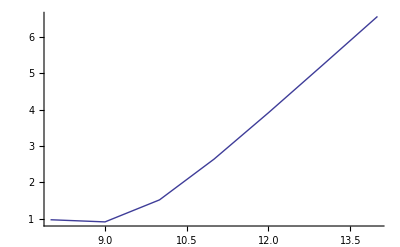

```mathematica
p1vsT=ListPlot[Log[10,resultvsT],Joined->True]
```

```mathematica
(Sqrt[3]*Pi*1.0)^(4/3)
```

9.57078

{{100000000,222.395},{1000000000,9.07768},{10000000000,1.71609},{100000000000,1.06177},{1000000000000,0.945035},{10000000000000,0.925184},{100000000000000,0.92637}}

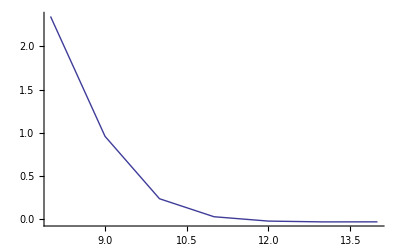

```mathematica
resulttestvsT=Table[{resultvsT[[ii,1]],resultvsT[[ii,2]]/((Sqrt[3]*Pi*kb*resultvsT[[ii,1]]/(me*c^2)*myb/Bc)^1.33)},{ii,1,NT}]
ListPlot[Log[10,resulttestvsT],Joined->True]
```

```mathematica
result=Table[{listBqed[[ii]],Q0synchnoqednew[10^(-10),10^10,listBqed[[ii]]*Bc,0]/Q0synchqedultrarelother[10^(-10),10^10,listBqed[[ii]]*Bc,0]},{ii,1,NB}]
```

{1/100,1/10,1,10,100,1000,10000,100000}

{{1/100,1.34072},{1/10,3.8072},{1,32.7255},{10,586.473},{100,12250.9},{1000,262344.},{10000,5.64482×10^6},{100000,1.21581×10^8}}

```mathematica
myT=10^12;
resultotherT=Table[{listBqed[[ii]],Q0synchnoqednew[10^(-10),myT,listBqed[[ii]]*Bc,0]/Q0synchqedultrarelother[10^(-10),myT,listBqed[[ii]]*Bc,0]},{ii,1,NB}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{1/100,29.1587},{1/10,425.282},{1,8237.47},{10,174433.},{100,3.74997×10^6},{1000,8.0762×10^7},{10000,1.73984×10^9},{100000,3.74832×10^10}}

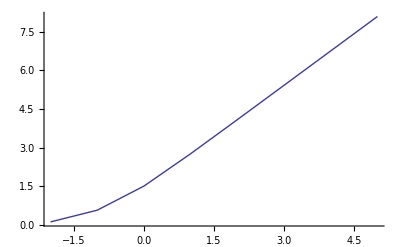

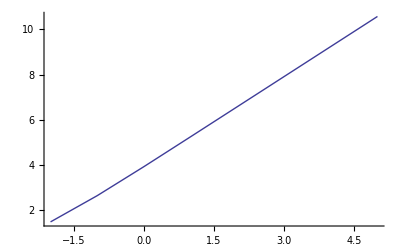

```mathematica
p1=ListPlot[Log[10,result],Joined->True]
p2=ListPlot[Log[10,resultotherT],Joined->True]
```

{{1/100,32.393},{1/10,4.26957},{1,1.70346},{10,1.41697},{100,1.37387},{1000,1.36557},{10000,1.36383},{100000,1.36346}}

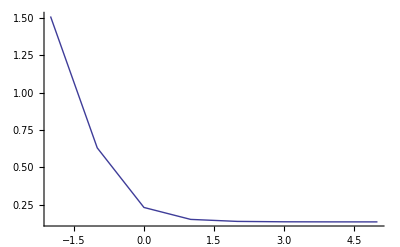

```mathematica
myT=10^(10);
resulttest=Table[{result[[ii,1]],result[[ii,2]]/(Sqrt[3]*Pi*kb*myT/(me*c^2)*result[[ii,1]])^(4/3)},{ii,1,NB}]
p3=ListPlot[Log[10,resulttest],Joined->True]
```

{{1/100,1.5178},{1/10,1.02752},{1,0.923788},{10,0.907976},{100,0.906023},{1000,0.905702},{10000,0.905638},{100000,0.905624}}

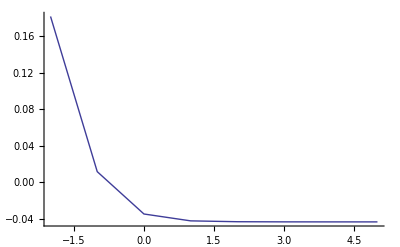

```mathematica
myT=10^(12);
resulttest=Table[{resultotherT[[ii,1]],resultotherT[[ii,2]]/(Sqrt[3]*Pi*kb*myT/(me*c^2)*resultotherT[[ii,1]])^(4/3)},{ii,1,NB}]
p3=ListPlot[Log[10,resulttest],Joined->True]
```